Fixpunkte des Ratengleichungssystems ohne Feedback (Ν ist hier ein griechisches Nu):

```mathematica
Solve[{0==Ν S-S/τs,0==(J-Ν)/τn-Ν S},{S,Ν}]
```

{{S→0,Ν→J},{S→(-1+J τs)/τn,Ν→1/τs}}

Jacobi-Matrix:

```mathematica
M=FullSimplify[D[{Ν S-S/τs,(J-Ν)/τn-Ν S},{{S,Ν}}]];
MatrixForm[M]
```

(Ν-1/τs | S
-Ν | -(1+S τn)/τn)

Fixpunkt x_1^* in Jacobi-Matrix einsetzen:

```mathematica
S=0;Ν=J;
MatrixForm[M]
```

(J-1/τs | 0
-J | -1/τn)

Variablen S und Ν wieder freigeben, um zweiten Fixpunkt x_2^* einsetzen zu können:

```mathematica
S=.;Ν=.;
```

Fixpunkt x_2^* in Jacobi-Matrix einsetzen:

```mathematica
S=(τs J-1)/τn;Ν=1/τs;
MatrixForm[M]
```

(0 | (-1+J τs)/τn
-1/τs | -(J τs)/τn)

Bestimmung der Eigenwerte:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
M=FullSimplify[D[{Ν S-S/τs,(J-Ν)/τn-Ν S},{{S,Ν}}]];
S=(τs J-1)/τn;Ν=1/τs;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1]
λ2=Part[EV,2]
```

-(J τs+(√(4 τn-4 J τn τs+J^2 τs^3))/(√τs))/(2 τn)

-(J τs-(√(4 τn-4 J τn τs+J^2 τs^3))/(√τs))/(2 τn)

Eigenwerte als Funktion von S schreiben (S vom zweiten Fixpunkt nach J umstellen):

```mathematica
S=.;J=(1+τn S)/τs;
FullSimplify[λ1]
FullSimplify[λ2]
```

-(1+S τn+(√(-4 S τn^2+(1+S τn)^2 τs))/(√τs))/(2 τn)

-(1+S τn-(√(-4 S τn^2+(1+S τn)^2 τs))/(√τs))/(2 τn)

Stabilitätsanalyse bezüglich J:
Prüfen der Stabilität der Eigenwerte für positive Diskriminante, bzw. für reelen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach J:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
Solve[J τs+(√(4 τn-4 J τn τs+J^2 τs^3))/(√τs)==0,J]
Solve[J τs-(√(4 τn-4 J τn τs+J^2 τs^3))/(√τs)==0,J]
```

{}

{{J→1/τs}}

Bei welchem J wird die Diskriminante Null?

```mathematica
Solve[4 τn-4 J τn τs+J^2 τs^3==0,J]
```

{{J→(2 (τn τs-√(τn^2 τs^2-τn τs^3)))/τs^3},{J→(2 (τn τs+√(τn^2 τs^2-τn τs^3)))/τs^3}}

Prüfen der Stabilität der Eigenwerte für negative Diskriminante, bzw. für komplexen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach J:

```mathematica
Solve[J τs==0,J]
```

{{J→0}}

Setzen der Parameter für das Bifurkationsdiagramm λ(J):

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
M=FullSimplify[D[{Ν S-S/τs,(J-Ν)/τn-Ν S},{{S,Ν}}]];
S=(τs J-1)/τn;Ν=1/τs;
τs=10^-2;
τn=10^-2;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1];
λ2=Part[EV,2];
```

Eigenwerte in Abhängigkeit von J:

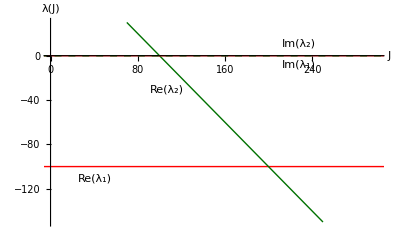

```mathematica
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{J,-1000,1000},AxesLabel->{"J","λ(J)"},PlotRange->{{0,300},{-150,30}},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.15,.23}]],Text["Re(λ_2)",Scaled[{.36,.66}]],Text["Im(λ_1)",Scaled[{.75,.78}]],Text["Im(λ_2)",Scaled[{.75,0.88}]]}]
```

Stabilitätsanalyse bezüglich S:
Prüfen der Stabilität der Eigenwerte für positive Diskriminante, bzw. für reelen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach S:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
Solve[1+S τn+(√(-4 S τn^2+(1+S τn)^2 τs))/(√τs)==0,S]
Solve[1+S τn-(√(-4 S τn^2+(1+S τn)^2 τs))/(√τs)==0,S]
```

{}

{{S→0}}

Bei welchem S wird die Diskriminante Null?

```mathematica
Solve[-4 S τn^2+(1+S τn)^2 τs==0,S]
```

{{S→(2 τn^2-τn τs-2 √(τn^4-τn^3 τs))/(τn^2 τs)},{S→(2 τn^2-τn τs+2 √(τn^4-τn^3 τs))/(τn^2 τs)}}

Prüfen der Stabilität der Eigenwerte für negative Diskriminante, bzw. für komplexen Eigenwert, durch Nullsetzen ihrer Realteile und Auflösen nach S:

```mathematica
Solve[1+S τn==0,S]
```

{{S→-1/τn}}

Setzen der Parameter für das Bifurkationsdiagramm λ(S):

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
M=FullSimplify[D[{Ν S-S/τs,(J-Ν)/τn-Ν S},{{S,Ν}}]];
S=(τs J-1)/τn;Ν=1/τs;
τs=10^-2;
τn=10^-2;
EV=FullSimplify[Eigenvalues[M]];
λ1=Part[EV,1];
λ2=Part[EV,2];
S=.;J=(1+τn S)/τs;
FullSimplify[λ1];
FullSimplify[λ2];
```

Eigenwerte in Abhängigkeit von S:

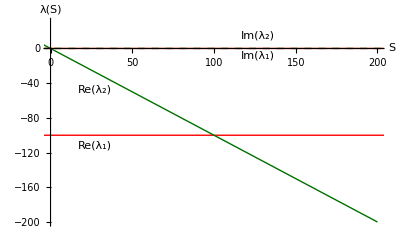

```mathematica
Plot[{Re[λ1],Re[λ2],Im[λ1],Im[λ2]},{S,-1000,1000},AxesLabel->{"S","λ(S)"},PlotRange->{{0,200},{-200,30}},PlotStyle->{Red,Darker[Darker[Green]],Red,{Darker[Darker[Green]],Dashed}},Epilog->{Text["Re(λ_1)",Scaled[{.15,.39}]],Text["Re(λ_2)",Scaled[{.15,.66}]],Text["Im(λ_1)",Scaled[{.63,.82}]],Text["Im(λ_2)",Scaled[{.63,0.92}]]}]
```

Zeitverläufe S(t) und Ν(t), Phasenraumportrait S(Ν) mit Berücksichtigung des Terms für spontane Emission:

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
β=0.01;
τs=10^-2;
τn=10^-2;
J=150;
tmax=100;
Sfix=(τs J-1)/τn;Νfix=1/τs;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
s=NDSolve[{S'[t]==Ν[t] S[t]-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J-Ν[t])/τn-Ν[t] S[t],S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev},{S,Ν},{t,0,tmax}];
```

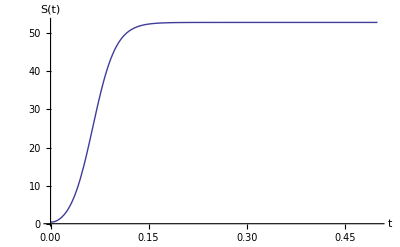

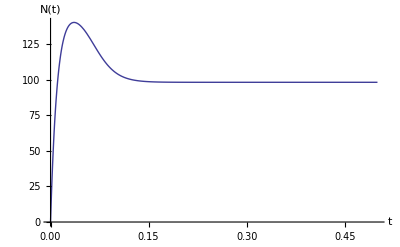

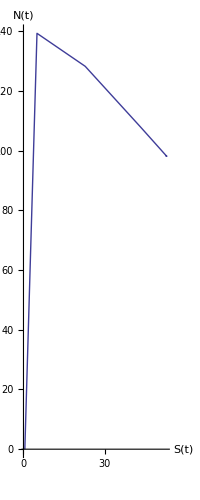

```mathematica
Plot[Evaluate[S[t]/.s],{t,0,tmax/200},AxesLabel->{"t","S(t)"},PlotRange->All]
Plot[Evaluate[Ν[t]/.s],{t,0,tmax/200},AxesLabel->{"t","N(t)"},PlotRange->All]
ParametricPlot[Evaluate[{S[t],Ν[t]}/.s],{t,0,tmax},AxesLabel->{"S(t)","Ν(t)"},PlotRange->All]
```

Input-Output-Kurve S(J):

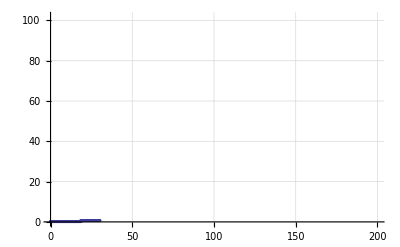

```mathematica
S=.;Ν=.;τs=.;τn=.;β=.;J=.;
β=0.01;
τs=10^-2;
τn=10^-2;
tmax=100;
Jmax=200;
step=0.1;
Sfix=0.01;Νfix=J;
Sdev=-0.99 Sfix;
Νdev=-Νfix;
a=Range[0];

ProgressIndicator[Dynamic[J],{0,Jmax}]
Do[s=NDSolve[{S'[t]==Ν[t] S[t]-S[t]/τs+(β Ν[t])/τn,Ν'[t]==(J-Ν[t])/τn-Ν[t] S[t],S[0]==Sfix+Sdev,Ν[0]==Νfix+Νdev},{S,Ν},{t,0,tmax}];a=Flatten[Append[a,{J,Evaluate[S[tmax]/.s]}]],{J,0,Jmax,step}];
io=Partition[a,2];
ListPlot[io,AxesLabel->{"J","S(J)"},PlotMarkers->{●,3},GridLines->Automatic]
```